```mathematica
(* 
 This is a simple example of plotting different combinations of variables where each are stored as a vector David Stuart, January 2013
*)

(* 
 First we need the error bar plotting package 
*)
Needs["ErrorBarPlots`"];
```

```mathematica
(* 
 Next we define the data for each variable as vectors, which is a bunch of points of (a,b) with an uncertainty for b of db.
*)
```

```mathematica
a={1,2,3,4,5};
b={0.1,1.95,4.1,6.0,9.1};
db={0.06,0.05,0.04,0.3,1.8};

(* 
 First let's make a simple plot of y vs x by making a table of the data and plotting it 
*)
xy=Table[{a[[i]],b[[i]]},{i,1,Length[a]}];
```

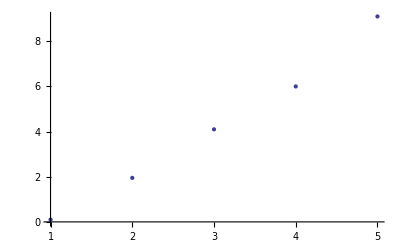

```mathematica
ListPlot[xy]
```

```mathematica
(* 
 Now, fit the data to a simple line and then overlay the fitted function and the original data using the Show command.
*)
linearFit = Fit[xy,{1,x}, x];
```

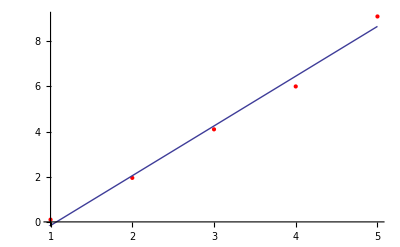

```mathematica
Show[ListPlot[xy,PlotStyle->Red],Plot[linearFit,{x,0,5}]]
```

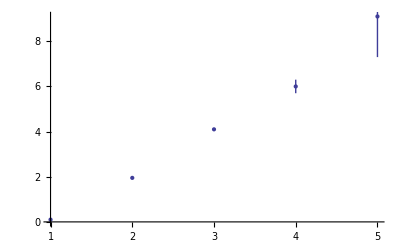

```mathematica
(* 
 But that fit and plot did not include the error bars. We do that now by making a Table including the error bar specification 
*)
xyerr=Table[{{a[[i]],b[[i]]},ErrorBar[db[[i]]]},{i,1,Length[a]}];

(* And plot it using ErrorListPlot *)
ErrorListPlot[xyerr]
```

```mathematica
(* 
 Do a non-linear fit including the uncertainties. The uncertainties are handled as weights which are 1/error^2. 
*)
fitResult = NonlinearModelFit[xy,intercept+slope*x,{{intercept,1.},{slope,2.}},x, Weights->1/db^2]
```

FittedModel[-1.98901+2.01873 x]

```mathematica
fitResult["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
intercept | -1.98901 | 0.120628 | -16.4887 | 0.000485502
slope | 2.01873 | 0.049873 | 40.4774 | 0.0000331802

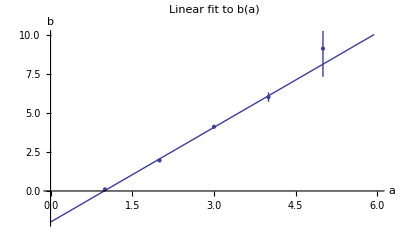

```mathematica
Show[
Plot[fitResult[x],{x,0,6}, PlotLabel->"Linear fit to b(a)",AxesLabel->{"a","b"},PlotRange->{-2.,10.}],
ErrorListPlot[xyerr]]
```

```mathematica
(* 
 Print the 68% confidence level for each of the parameters 
*)
fitResult["ParameterConfidenceIntervals",ConfidenceLevel->0.68]
```

{{-2.13242,-1.84559},{1.95944,2.07803}}

```mathematica
(* 
Now calculate the residuals which are how far each point is from the fitted value.
*)

(* 
First get the simple residuals directly from the fit 
*)
```

```mathematica
resid = fitResult["FitResiduals"]
```

{0.0702755,-0.0984554,0.0328138,-0.0859171,0.995352}

```mathematica
(* 
Then get the residuals with uncertainties for easier plotting 
*)
residWithErrors = Table[{{xy[[i,1]],xy[[i,2]] - fitResult[xy[[i,1]]]},ErrorBar[db[[i]]]},{i,1,Length[a]}];
```

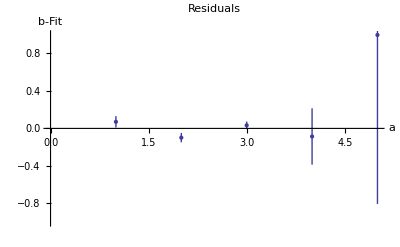

```mathematica
ErrorListPlot[residWithErrors, PlotLabel->"Residuals",PlotRange->{-1,1.}, AxesOrigin->{0,0}, AxesLabel->{"a","b-Fit"}]
```

```mathematica
(* Print a table of the output and confidence intervals *)
fitResult["SinglePredictionConfidenceIntervalTable", ConfidenceLevel->0.68]
```

Observed | Predicted | Standard Error | Confidence Interval
0.1 | 0.0297245 | 1.45225 | {-1.69689,1.75634}
1.95 | 2.04846 | 1.45091 | {0.323431,3.77348}
4.1 | 4.06719 | 1.45128 | {2.34172,5.79265}
6. | 6.08592 | 1.45337 | {4.35797,7.81387}
9.1 | 8.10465 | 1.45716 | {6.37219,9.8371}